```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.6.0X (December 23, 2020)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Guild[n]->{
Equation:>(r[Subscript[x, i]]-Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}])Subscript[n, i],Trait[x]->{Range->Interval[{-1,1}]}
}
}]
```

SetModel

transitions=Transitions

Auxs

Pops

Guilds

guilds={n}

Guild[n]={Equation:>(r[x_i]-∑_j^𝒩_n a[x_i,x_j] n_j) n_i,Trait[x]→{Range→Interval[{-1,1}]}}

old comps

comps[n]={n}

old traits

{gcomps[n], gtraits[n]={{n},{x}}

hi

```mathematica
EcoEvo`Private`eqn[Subscript[n, 1]]
```

n_1 (r[x_1]-∑_j^𝒩[n] a[x_1,x_j] n_j)

```mathematica
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
r[x_]:=1-x^2;
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]
```

{n_1'[t]==n_1[t] (1-x_1^2-n_1[t]-ⅇ^(-(x_1-x_2)^2/(2 σ^2)) n_2[t]),n_2'[t]==(1-x_2^2-ⅇ^(-(-x_1+x_2)^2/(2 σ^2)) n_1[t]-n_2[t]) n_2[t]}

{n_1'[t]==n_1[t] (1-x_1^2-n_1[t]-ⅇ^(-1/2 (x_1-x_2)^2) n_2[t]),n_2'[t]==(1-x_2^2-ⅇ^(-1/2 (-x_1+x_2)^2) n_1[t]-n_2[t]) n_2[t]}

calling EcoEqns...

calling NDSolve...

{}

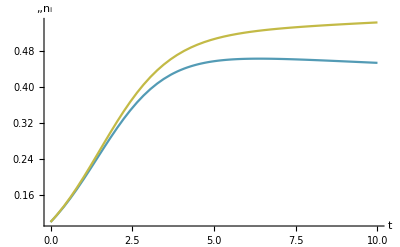

```mathematica
σ=1;
EcoEqns[{Subscript[𝒩, n]->2}]
sol=EcoSim[{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},10];
PlotDynamics[sol]
```

{n_1'[t]==n_1[t] (1-x_1^2-1. n_1[t]-ⅇ^(-12.5 (x_1-x_2)^2) n_2[t]),n_2'[t]==(1-x_2^2-ⅇ^(-12.5 (-x_1+x_2)^2) n_1[t]-1. n_2[t]) n_2[t]}

calling EcoEqns...

calling NDSolve...

{}

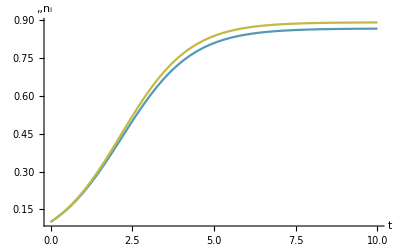

```mathematica
σ=0.2;
EcoEqns[{Subscript[𝒩, n]->2}]
sol=EcoSim[{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},10];
PlotDynamics[sol]
```

{n_1'[t]==n_1[t] (1-x_1^2-n_1[t]-ⅇ^(-1/8 (x_1-x_2)^2) n_2[t]),n_2'[t]==(1-x_2^2-ⅇ^(-1/8 (-x_1+x_2)^2) n_1[t]-n_2[t]) n_2[t]}

calling EcoEqns...

calling NDSolve...

{}

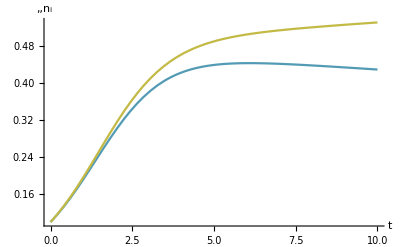

```mathematica
σ=2;
EcoEqns[{Subscript[𝒩, n]->2}]
sol=EcoSim[{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.2},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},10];
PlotDynamics[sol]
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.25,Subscript[x, 2]->0.2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n_1→0,n_2→0},{n_1→0.9375,n_2→0},{n_1→0,n_2→0.96},{n_1→0.0302853,n_2→0.930472}}

```mathematica
Clear[σ]
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]
```

{n_1'[t]==n_1[t] (1-x_1^2-n_1[t]-ⅇ^(-(x_1-x_2)^2/(2 σ^2)) n_2[t]),n_2'[t]==(1-x_2^2-ⅇ^(-(-x_1+x_2)^2/(2 σ^2)) n_1[t]-n_2[t]) n_2[t]}

## transitions

```mathematica
SetModel[{
Guild[n]->{
Components->{n1,n2},
Traits->{x}
},
Transitions->{
{{Subscript[n1, i]⇒∅},-d1[Subscript[x[n1], i]] Subscript[n1, i]},
{{Subscript[n2, i]⇒∅},-d2[Subscript[x[n2], i]] Subscript[n2, i]},
{{0 Subscript[n1, i]⇒Subscript[n1, i]},b Subscript[n1, i],NormalDistribution[0,σμ]},
{{0 Subscript[n2, i]⇒Subscript[n2, i]},b Subscript[n2, i],NormalDistribution[0,σμ]},
{{Subscript[n1, i]⇒Subscript[n2, i]},d12 Subscript[n1, i]},
{{Subscript[n2, i]⇒Subscript[n1, i]},d21 Subscript[n2, i]}
}
}]
```

SetModel

transitions={{{n1_i⇒∅},-d1[x[n1]_i] n1_i},{{n2_i⇒∅},-d2[x[n2]_i] n2_i},{{0 n1_i⇒n1_i},b n1_i,NormalDistribution[0,σμ]},{{0 n2_i⇒n2_i},b n2_i,NormalDistribution[0,σμ]},{{n1_i⇒n2_i},d12 n1_i},{{n2_i⇒n1_i},d21 n2_i}}

proc={{{{n1_i→-1+n1_i,∅→1+∅}},-d1[x[n1]_i] n1_i},{{{n2_i→-1+n2_i,∅→1+∅}},-d2[x[n2]_i] n2_i},{{{n1_i→n1_i,n1_i→1+n1_i}},b n1_i,NormalDistribution[0,σμ]},{{{n2_i→n2_i,n2_i→1+n2_i}},b n2_i,NormalDistribution[0,σμ]},{{{n1_i→-1+n1_i,n2_i→1+n2_i}},d12 n1_i},{{{n2_i→-1+n2_i,n1_i→1+n1_i}},d21 n2_i}}

rules={{{n1_i→-1+n1_i,∅→1+∅}},{{n2_i→-1+n2_i,∅→1+∅}},{{n1_i→n1_i,n1_i→1+n1_i}},{{n2_i→n2_i,n2_i→1+n2_i}},{{n1_i→-1+n1_i,n2_i→1+n2_i}},{{n2_i→-1+n2_i,n1_i→1+n1_i}}}

rates={-d1[x[n1]_i] n1_i,-d2[x[n2]_i] n2_i,b n1_i,b n2_i,d12 n1_i,d21 n2_i}

eqns={n1_i→b n1_i-d12 n1_i+d1[x[n1]_i] n1_i+d21 n2_i,∅→-d1[x[n1]_i] n1_i-d2[x[n2]_i] n2_i,n2_i→d12 n1_i+b n2_i-d21 n2_i+d2[x[n2]_i] n2_i}

Auxs

Pops

Guilds

guilds={n}

Guild[n]={Components→{n1,n2},Traits→{x}}

new comps

ReplaceAll::reps: {Guild[n]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

comps[n]={n1,n2}

new traits

ReplaceAll::reps: {Guild[n]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{gcomps[n], gtraits[n]={{n1,n2},{x}}

ReplaceAll::reps: {Trait[x,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

ColorData::notent: Color/.Join[Trait[x],{Components→{n1,n2},Traits→{x}},{Color→EEReds}] is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

Join::heads: Heads Trait and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
EcoEvo`Private`eqn[Subscript[n1, 1]]
```

b n1_1-d12 n1_1+d1[x[n1]_1] n1_1+d21 n2_1

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]
```

{n1_1'[t]==b n1_1[t]-d12 n1_1[t]+d1[x[n1]_1] n1_1[t]+d21 n2_1[t],n2_1'[t]==d12 n1_1[t]+b n2_1[t]-d21 n2_1[t]+d2[x[n2]_1] n2_1[t],n1_2'[t]==b n1_2[t]-d12 n1_2[t]+d1[x[n1]_2] n1_2[t]+d21 n2_2[t],n2_2'[t]==d12 n1_2[t]+b n2_2[t]-d21 n2_2[t]+d2[x[n2]_2] n2_2[t]}

```mathematica
TraitsQ[{Subscript[x[n1], 1]->0.1,Subscript[x[n2], 1]->0.2}]
```

False